#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan/results

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

“data”=dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976)

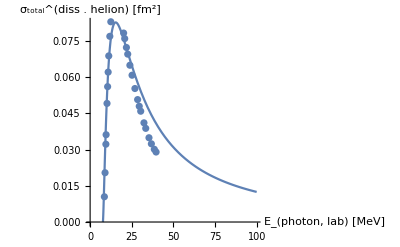

```mathematica
He3DatamBarn=Import["../../../data/triton_inclusive_photo_abs.csv","Data"];
He3DatamBarnGibson=Import["../../../data/he3_photo_diss_sigma_gibson.dat","Data"];
He3DataFm2=Transpose[{Transpose[He3DatamBarnGibson][[1]],Transpose[He3DatamBarnGibson][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=2 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,7.67,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5,1.5};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];

thresholdLIT=(10.8)^(-6);
thresholdD=thresholdLIT;
```

```mathematica
Clear[matSqrts];matSqrts[norm_,cutoff_:0]:=Block[{es=Eigensystem[norm],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[es[[1]],#<cutoff&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]
```

### Read LHS ⟨ ϕ_D^n|(Ĥ)_(V18+UIX)|ϕ_D^m ⟩, m,n∈{1,N_D}

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}];
```

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,0.2];
```

min/max: {1.66761×10^-14,86.2243}

(min/max) discarded elements: 1247 {1.66761×10^-14,0.194754}

#### The real calculation

Set a sensible cut-off

min/max: {1.66761×10^-14,86.2243}

(min/max) discarded elements: 451 {1.66761×10^-14,6.26557×10^-7}

B(^3He) = -7.69929

Dim_full^helion = 1440=^!1440   ;     Dim_(non - singular)^helion = 989

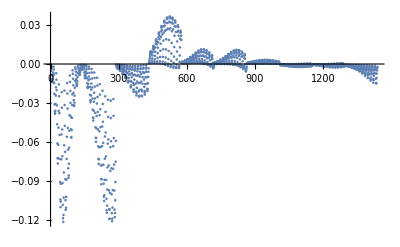

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdD];

{e0,v0}=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0][[1]]]
fullv0=Normalize[Transpose[He3Nmh].v0];
ListPlot[Re[fullv0],PlotRange->Full]
```

#### Read LHS ⟨ ϕ_lit^n|(Ĥ)_(V18+UIX)|ϕ_lit^m ⟩, m,n∈{1,N_LIT}

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_LIT = ",LITbasisDim];
```

N_LIT = {1280,2048}

min/max: {-1.93879×10^-15,114.22}

(min/max) discarded elements: 646 {-1.93879×10^-15,5.89327×10^-7}

J=0.5:  E_0=-2.18567

min/max: {-2.1037×10^-15,87.9909}

(min/max) discarded elements: 1034 {-2.1037×10^-15,6.25597×10^-7}

J=1.5:  E_0=-2.15736

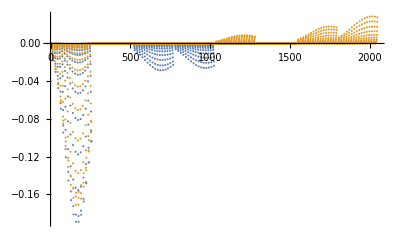

```mathematica
LitNmhis={};
fullv0l={};
Do[
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
AppendTo[LitNmhis,{LitNmh,LitNmhi}];
{e0l,v0l}=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&][[1]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,Normalize[Transpose[LitNmh].v0l]];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

ListPlot[Re[fullv0l],PlotRange->Full]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];
CouplingBlock={};
Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];

CouplingBlocks={};
Do[
Print["m_L=",mL];
If[Sign[mIn]>=0,mJLIT=StringPadRight[StringDelete[ToString[mIn],"."],2,"0"],mJLIT=StringPadRight[StringDelete[ToString[mIn],"."],3,"0"]];
If[Sign[mL]>=0,mMUL=StringPadRight[StringDelete[ToString[mL],"."],2,"0"],mMUL=StringPadRight[StringDelete[ToString[mL],"."],3,"0"]];

files="./"<>ToString[#]<>"_S_"<>JLIT<>"_"<>mJLIT<>"_"<>mMUL<>".lit"&/@ks;
inhomos=readREAL8list[#]&/@files;
CouplingMatrices=ArrayReshape[#,{Sqrt[Length[#]],Sqrt[Length[#]]}]&/@inhomos;
CouplingBloxx=#[[He3BasisDim+1;;,;;He3BasisDim]]&/@CouplingMatrices;
dims=Dimensions[#]&/@CouplingBloxx;
coupl=ClebschGordan[{multipolarity,mL},{J0,mIn-mL},{Subscript[I, n][[nj]],mIn}];
(*Print["⟨",multipolarity,mL,J0,mIn-mL,"|",Subscript[I, n][[nj]],mIn,"⟩ =  ",coupl];*)
(*Print[ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],DBasisDim}]//MatrixForm];*)
AppendTo[CouplingBlocks,coupl ArrayReshape[CouplingBloxx,{Total[dims[[All,1]]],He3BasisDim}]];
,{mL,mM}
]

AppendTo[CouplingBlock,{mIn,Total[CouplingBlocks]}];
(*Print["m_I_n=",mIn,"  : ",Total[CouplingBlocks]//MatrixForm];*)
,{mIn,mIns[[nj]]}]

AppendTo[CouplingBlockj,CouplingBlock];
,{nj,Range[1,Length[Subscript[I, n]]]}]

Print["Dim(⟨ψ|ο̂|helion⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

m_L=-1

m_L=0

m_L=0

m_L=1

m_L=-1

m_L=-1

m_L=0

m_L=0

m_L=1

m_L=1

Dim(⟨ψ|ο̂|helion⟩) = {2}

Dim(⟨ψ|Ĥ|ψ⟩) = {2}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {2}

#### Analysis of RHS

```mathematica
thrs=10^(-7);
OμRHS=normreg[thrs,He3Norm];
{λsHe,trfHe}=Eigensystem[(Transpose[OμRHS].He3Ham).OμRHS];
evgs=Flatten[trfHe[[TakeSmallest[λsHe->"Index",1]]]];
inhomo={};
Do[
Do[
OμLHS=normreg[thrs,LitNorm[[nj]]];
{λfinal,trfLit}=Eigensystem[(Transpose[OμLHS].LitHam[[nj]]).OμLHS];
tmp=CouplingBlockj[[nj]][[mm]][[2]];
AppendTo[inhomo,(Transpose[OμLHS].(tmp.OμRHS)).evgs];
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
mm=1;
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
inhomonorms=Table[Norm[#[[;;n]]],{n,Length[#]}]&/@inhomo;
ListPlot[inhomonorms,AxesLabel->{"Basis Dimension N","∑_(n=1)^N |n rY_1^3 He|^2"},PlotLegends->lege,ImageSize->ImgSize,PlotRange->{Automatic,{0,1}}]
```

Set::shape: Lists {λsHe,trfHe} and Eigensystem[Transpose[normreg[1/10000000,{{1.,0.949972,0.818031,0.644801,0.471382,0.325364,0.216234,0.140576,0.0903111,0.057662,0.0366993,0.0233192,0.877788,0.786642,0.642605,0.492597,0.360595,0.253426,0.171633,0.11299,0.0730694,0.0467954,0.0298217,0.018959,0.609619,0.531083,0.412558,0.299485,0.211084,0.146975,0.100946,0.0678788,0.0446316,0.0288593,0.0184782,0.011772,0.355242,0.311387,0.23888,0.167075,0.111865,0.0744302,0.0500144,0.0338153,0.0226924,0.0149702,0.00971169,0.00622987,0.186501,0.164938,«1390»},«49»,«1390»}]].{«1»}.normreg[1/10000000,{{1.,0.949972,0.818031,0.644801,0.471382,0.325364,0.216234,«38»,0.0149702,0.00971169,0.00622987,0.186501,0.164938,«1390»},{«1»},«48»,«1390»}]] are not the same shape.

TakeSmallest::rvec2: Input λsHe is not a real-valued vector.

Part::pkspec1: The expression TakeSmallest[λsHe→Index,1] cannot be used as a part specification.

Set::shape: Lists {λfinal,trfLit} and Eigensystem[Transpose[normreg[1/10000000,{{1.,0.95231,0.825482,0.657848,0.488665,0.343364,0.231338,0.151147,0.0966155,0.060819,0.0378819,0.0234248,0.0144135,0.00883919,0.00540836,0.00330417,0.961346,0.909927,0.78433,0.622047,0.460273,0.322445,0.216761,0.141397,0.0902812,0.0567871,0.0353516,0.0218521,0.0134425,0.00824218,0.00504263,0.00308036,0.857506,0.806639,0.691414,0.545745,0.402267,0.28098,0.188476,0.122754,0.0782913,0.0492079,0.0306173,0.0189188,0.0116353,0.00713296,0.0043634,0.00266528,0.717142,0.670299,«1230»},«49»,«1230»}]].«1».normreg[1/10000000,{{1.,0.95231,0.825482,0.657848,0.488665,0.343364,0.231338,«38»,0.00713296,0.0043634,0.00266528,0.717142,0.670299,«1230»},«49»,«1230»}]] are not the same shape.

Set::shape: Lists {λfinal,trfLit} and Eigensystem[Transpose[normreg[1/10000000,{{1.,0.949681,0.816745,0.643182,0.470846,0.32557,0.215729,0.138622,0.0871706,0.0540042,0.0331177,0.0201696,0.0122271,0.0073892,0.00445623,0.00268378,0.961335,0.907096,0.775532,0.607663,0.443058,0.30542,0.201925,0.129546,0.0813735,0.0503745,0.0308758,0.0187979,0.0113929,0.00688395,0.00415116,0.00249973,0.857467,0.803829,0.68321,0.532669,0.386843,0.265869,0.175392,0.112349,0.0704955,0.0436083,0.0267152,0.0162593,0.00985211,0.00595204,0.00358879,0.00216103,0.717068,0.667697,«1998»},«49»,«1998»}]].{{1741.77,1652.06,1419.2,1116.55,816.756,564.425,«39»,7.25789,4.37604,2.63503,754.463,701.013,«1998»},{«1»},«48»,«1998»}.normreg[1/10000000,{«1»}]] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

-Graphics-

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

```mathematica
(*SetSharedVariable[testcompo,testfu]*)
σI=4.0;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
testfu=0;
```

```mathematica
Clear[normreg];
normreg[threshold_,noMa_]:=Block[
{es=Eigensystem[noMa],μ,transf},
{μ,transf}=Transpose[Select[Transpose[es],#[[1]]>threshold&]];
(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];

Clear[decompose];
decompose[thresholdD_,thresholdLIT_,He3Norm_,He3Ham_,LITNorm_,LITHam_,LITYD_]:= Block[{OμRHS,λsD,trfD,OμLHS,λfinal,trfLit,inhomo,egs,evgs},
OμRHS=normreg[thresholdD,He3Norm];
{λsD,trfD}=Eigensystem[(Transpose[OμRHS].He3Ham).OμRHS];
egs=Min[λsD];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];

OμLHS=normreg[thresholdLIT,LITNorm];

{λfinal,trfLit}=Eigensystem[(Transpose[OμLHS].LITHam).OμLHS];

Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(D,LIT) = ",Dimensions[λsD],Dimensions[λfinal]];

inhomo=(Transpose[OμLHS].(LITYD.OμRHS)).evgs;
{λfinal,(trfLit.inhomo)^2,egs}
];

Clear[litcomp];
litcomp[thresholdD_,thresholdLIT_,He3Norm_,He3Ham_,LITNorm_,LITHam_,LITYD_]:=Block[{λscf=decompose[thresholdD,thresholdLIT,He3Norm,He3Ham,LITNorm,LITHam,LITYD]},
egrnd=λscf[[3]];
tmpp=Transpose[λscf[[;;2]]];
Plus@@((#[[2]]/(Abs[#[[1]]-egrnd-σRe]^2+σI^2))&/@tmpp)];
```

```mathematica
Clear[LIT,LITs,testfu];

minth=thresholdLIT;maxth=.02 thresholdLIT;nth=1;
If[nth==1,thresholdrng={thresholdLIT},thresholdrng=Range[minth,maxth,(maxth-minth)/nth]];

LITsj={};

Do[
testfu={};
Print["I_n=",Subscript[I, n][[nj]],"  J_0=",J0];
Do[

tmp=CouplingBlockj[[nj]][[mm]][[2]];

AppendTo[testfu,(-1)^(Subscript[I, n][[nj]]-J0) Evaluate[litcomp[#,#,He3Norm,He3Ham,LitNorm[[nj]],LitHam[[nj]],tmp]&/@thresholdrng]];
,{mm,Length[mIns[[nj]]]}
];

AppendTo[LITsj,Total[testfu]/.σRe->σRs];
,{nj,Range[1,Length[Subscript[I, n]]]}
]

thrlegend=("λ_𝟙="<>ToString[#,TraditionalForm]&/@thresholdrng);
pltlabs="I_n="<>ToString[#]&/@Subscript[I, n]

plote=ListPlot[Flatten[(Transpose[{σRs,#}]&/@LITsj[[#]])&/@Range[1,Length[Subscript[I, n]]],1],
PlotLabel->Style["σ_I = "<>ToString[σI]<>"    ; J_lit = "<>ToString[Subscript[I, n]],18,Red],
AxesLabel->{Style["σ_R [MeV]",Gray,18],Style["LIT [MeV^-4]",Red,18]},
PlotLegends->Placed[thrlegend,Above],
LabelStyle->12,ImageSize->ImgSize,PlotRange->Full,PlotLabels->Placed[pltlabs,Above],
Mesh->5,MeshFunctions->{#2&,#2&,#2&},PlotMarkers->{Automatic,Scaled[0.01 #]}&/@Range[1,nth],
Joined->True];
Export["plot.pdf",plote,"PDF","AllowRasterization"->False]
```

I_n=0.5  J_0=0.5

E_0( th=6.3017×10^-7 ) = -7.69929    dim(D,LIT) = {989}{634}

E_0( th=6.3017×10^-7 ) = -7.69929    dim(D,LIT) = {989}{634}

I_n=1.5  J_0=0.5

E_0( th=6.3017×10^-7 ) = -7.69929    dim(D,LIT) = {989}{1014}

E_0( th=6.3017×10^-7 ) = -7.69929    dim(D,LIT) = {989}{1014}

E_0( th=6.3017×10^-7 ) = -7.69929    dim(D,LIT) = {989}{1014}

«1 more identical outputs»

{I_n=0.5,I_n=1.5}

plot.pdf

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

E_0( th=6.3017×10^-7 ) = -7.69929    dim(He3,LIT) = {989}{634}

E_0( th=6.3017×10^-7 ) = -7.69929    dim(He3,LIT) = {989}{1014}

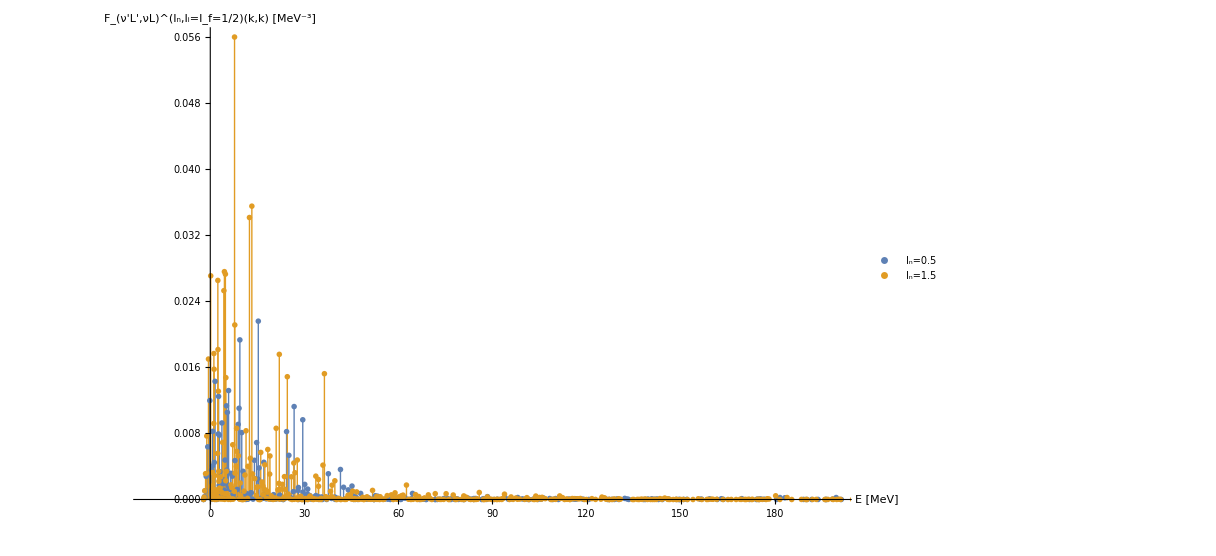
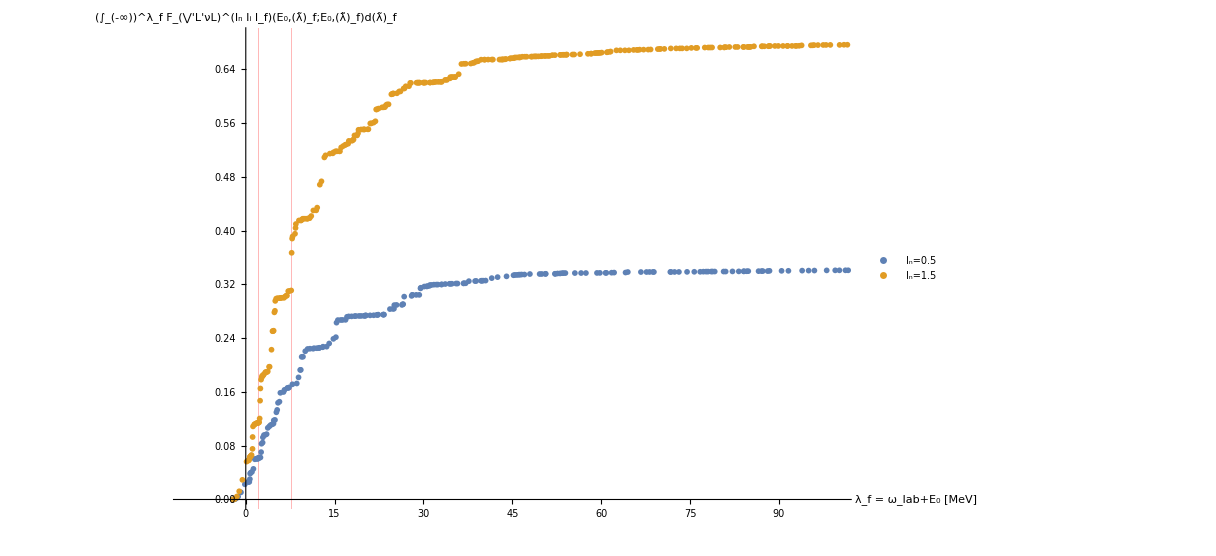

delta_strength_function_helion.pdf

```mathematica
Clear[thresh,es,μ,transf];
lpsis={};CumStrengths={};

es=Eigensystem[He3Norm];
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>thresholdD&]];
OμRHS=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);

{λsD,trfD}=Eigensystem[(Transpose[OμRHS].He3Ham).OμRHS];
evgs=Flatten[trfD[[TakeSmallest[λsD->"Index",1]]]];
egs=Min[λsD];
leg={};
Do[
lpsi={};
esl=Eigensystem[LitNorm[[nj]]];
{μl,transfl}=Transpose[Select[Transpose[esl],Re[#[[1]]]>thresholdLIT&]];
OμLHS=(Transpose[transfl].DiagonalMatrix[μl^(-1/2)]);
{λfinal,trfLit}=Eigensystem[(Transpose[OμLHS].(LitHam[[nj]])).OμLHS];

Print["E_0( th=",N[thresholdD]," ) = ",egs,"    dim(He3,LIT) = ",Dimensions[λsD],Dimensions[λfinal]];

tmpl=0;
Do[
inhomo=(Transpose[OμLHS].(CouplingBlockj[[nj]][[mm]][[2]].OμRHS)).(evgs);
(*AppendTo[lpsi,Transpose[{λfinal(*+Abs[egs]*),(trfLit.inhomo)^2}]];*)
tmpl = tmpl + (trfLit.inhomo)^2;
,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsis,Transpose[{λfinal,tmpl}]];
AppendTo[CumStrengths,Transpose[{Sort[lpsis[[nj]]][[All,1]],Accumulate[Sort[lpsis[[nj]]][[All,2]]]}]];

AppendTo[leg,"I_n="<>ToString[Subscript[I, n][[nj]]]];

(*AppendTo[lpsis,Flatten[lpsi,1]];*)

,{nj,Range[1,Length[Subscript[I, n]]]}
]


plote3=Grid[{{
ListPlot[lpsis,Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{{-20,200},Full},AxesLabel->{Style["E [MeV]",18],Style["F_(ν'L',νL)^(I_n,I_i=I_f=1/2)(k,k) [MeV^-3]",18]},PlotStyle->{},PlotLegends->leg,ImageSize->ImgSize]
},{
ListPlot[CumStrengths,Joined->False,ImageSize->ImgSize,PlotRange->{{-10,100},Automatic},PlotLegends->leg,GridLines->{{{Abs[e0],Red},{Abs[e0l],Red}},None},AxesLabel->{Style["  λ_f = ω_lab+E_0 [MeV]",18],Style["(∫_(-∞))^λ_f F_(⋁'L'νL)^(I_n I_i I_f)(E_0,(λ̃)_f;E_0,(λ̃)_f)d(λ̃)_f",18]}]
}}]
Save[tmpDir<>"/lpsis.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],lpsis]
Save[tmpDir<>"/CumStrength.plot_"<>ToString[IntegerPart[AbsoluteTime[Now]-AbsoluteTime[Today]]],CumStrengths]
Export["delta_strength_function_helion.pdf",plote3,"PDF","AllowRasterization"->False]
```

#### S(E)=∑_m Ψ_m^2·δ(E-λ_m) → S_benign(E)

C(E):=∫E/0 dΔ S(Δ)=∑_(N_(n,d)) Poly[E,N_numerator]/Poly[E,N_denominator-1]
s.t. C_N/C_M=C(λ_(f,max))  (saturation criterium for equal polynomial orders in numerator and denominator)
F(E)=(∂C)/(∂E)

```mathematica
Put[CumStrengths,LocalObject["CumHelionStrengths"]]
```

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumHelionStrengths]

{(0.345916 t^5+0.636323 t^4+0.118388 t^3+0.080387 t^2+0.)/(1. t^5+2.99985 t^4+87.2967 t^3+38.4118 t^2+39.9577 t+0.00027907),(0.68768 t^5+0.751621 t^4+0.0460546 t^3+0.0276896 t^2+0.)/(1. t^5+2.46615 t^4+78.2715 t^3+21.2706 t^2+22.7312 t+0.000126803)}

{Piecewise[{{(2.22045×10^-16 t^9+0.401375 t^8+67.1761 t^7+1068.9 t^6+7616.84 t^5+30626.7 t^4+74579.7 t^3+109703. t^2+90114. t+31850.9)/((1. t^5+13.9282 t^4+161.295 t^3+801.214 t^2+1698.35 t+1300.66)^2), t≥-2.18567}, {0, True}}],Piecewise[{{(0.944304 t^8+123.857 t^7+1849.88 t^6+12464.9 t^5+47455.9 t^4+109430. t^3+152417. t^2+118557. t+39690.5)/((1. t^5+13.2529 t^4+146.095 t^3+697.124 t^2+1414.73 t+1034.09)^2), t≥-2.15736}, {0, True}}]}

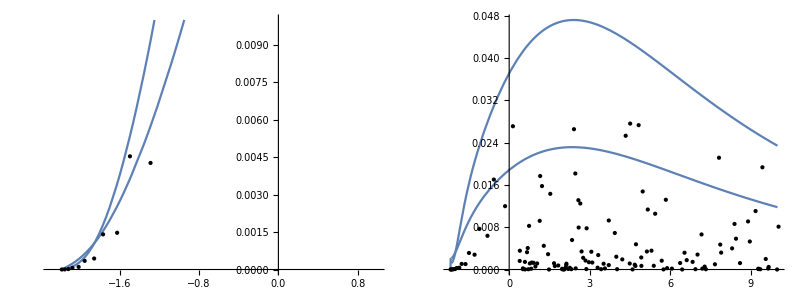

```mathematica
data=CumStrengths;
dataShifted=Transpose[{#[[All,1]]-#[[All,1]][[1]],#[[All,2]]}]&/@CumStrengths;
ordnum=5;orddenom=ordnum-1;
coffs={Array[cnum,ordnum],Array[cdenom,orddenom+1]};
inicoffs=Transpose[{Flatten[coffs],RandomReal[{0.0001,0.2},Length[Flatten[coffs]]]}];

(*num=Sum[coffs[[1]][[n]] (t)^n,{n,ordnum}]&/@Range[Length[data]];
denom=1+Sum[coffs[[2]][[n]] (t)^n,{n,orddenom}]&/@Range[Length[data]];*)
offsets=Min[#[[All,1]]]&/@data;
num=Sum[coffs[[1]][[n]] (t-0 #)^n,{n,2,ordnum}]&/@offsets;
denom=1+coffs[[2]][[-1]] t^ordnum+Sum[coffs[[2]][[n]] (t-0 #)^n,{n,orddenom}]&/@offsets;

model=num/denom;
constr=#>10.2^(-2)&/@Flatten[coffs];(*10.1^2>#>10.2^(-2)&/@Flatten[coffs];*)
constraints=Union[constr,{Abs[coffs[[1]][[-1]]/coffs[[2]][[-1]]-data[[#]][[-1]][[2]]]<10.^(-9)}]&/@Range[Length[data]];

wgts=Flatten[Join[{Differences[data[[#]]][[All,2]][[1]],Differences[data[[#]]][[All,2]]}]]&/@Range[Length[data]];
splitPoint=5;
origFac=121.;
wgt2=Join[origFac #[[;;splitPoint]],#[[1+splitPoint;;]]]&/@wgts;

optPOSsol=
NonlinearModelFit[dataShifted[[#]],{model[[#]],constraints[[#]]},inicoffs,t,Weights->wgt2[[#]],MaxIterations->2500]&/@Range[Length[data]];

CumFit[ee_]:=Piecewise[ {{optPOSsol[[#]][ee-offsets[[#]]],ee≥offsets[[#]]},{0,ee<offsets[[#]]}}]&/@Range[Length[optPOSsol]]
StC[em_]:=Piecewise[{{D[optPOSsol[[#]][t],t]/.t->(em-offsets[[#]]),em>=offsets[[#]]},{0,em<offsets[[#]]}}]&/@Range[Length[data]]

Simplify[#[t]]&/@optPOSsol//TraditionalForm
Simplify[#]&/@StC[t]//TraditionalForm

Grid[{{
Plot[CumFit[t-0 offsets[[#]]][[#]]&/@Range[Length[data]],{t,Min[offsets],110},Epilog->{PointSize[Small],Point[#]&/@CumStrengths},PlotRange->{{-2.3,1},{0,0.01}},ImageSize->ImgSize],
Plot[StC[e2],{e2,Min[offsets],10},Epilog->Map[Point,lpsis],PlotRange->Full,ImageSize->ImgSize]
}}]
```

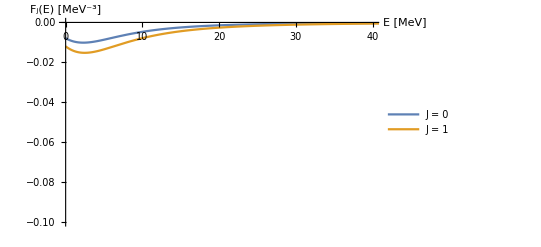

```mathematica
responseListJAren={};
responseListJ=StC[t];

jJtot={0,1};
Do[
responseListI={};
Do[
SixJ=SixJSymbol[{1,1,jJtot[[nj]]},{J0,J0,Subscript[I, n][[nIn]]}];
response=SixJ StC[t][[nIn]]/.t->e2;
AppendTo[responseListI,response];
,{nIn,Range[1,Length[Subscript[I, n]]]}
];
AppendTo[responseListJAren,Total[responseListI]];
,{nj,Range[Length[jJtot]]}
];

labeljlit=("J = "<>ToString[#])&/@jJtot;

Plot[responseListJAren,{e2,0,100},PlotRange->{{0,40},{-0.1,0}},PlotLegends->Placed[labeljlit,Bottom],AxesLabel->{"E [MeV]","F_j(E) [MeV^-3]"},LabelStyle->Directive[Larger]]
```

#### real and imaginary parts of the (generalized) polarizabilities from strength functions

{P_(if,J)^res(M^ν' L',M^ν L,k',k)}_imag=2 π^2 (-)^(L+I_f+I_i)L̂ L̂' [F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i+k)+(-)^(L+L'+J)F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i-k')]
The second term does not contribute because the initial state is the ground- and not an excited state!

ECCE: the L̂’s come from the multipole expansion of the plane wave as do the 2π’s
ImPList [I_(n=1),I_(n=2),...] [fit_1,fit_2,...] [k_0... k_max]

#### imaginary part of the amplitude and total photodisintegration cross-section

{T_(L_f λ_f;L_i λ_i)^(I_f M_f;I_i M_i)(k⃗',k⃗)}_imag=(-)^(1+λ_f+I_f-M_i) ∑_(M_L_f M_L_i J) (-)^(L_i+L_f) (L̂)^2(I_f | J | I_i
-M_f | m | M_i) (L_i | L_f | J
M_i | M_f | -m) {P_(if,J)^(L_f λ_f,L_i λ_i)(k',k)}_imag D_(M_f,-λ_f)^L_f(0,θ,0) 

ECCE: 
i)   the polarization λ affects magnetic multipole ME’s, only (see eqs. (27,29,41) )
ii)  k⃗||(e⃗)_z ⇒ D_(M,λ)^L(R)=1
iii) fm^2=10^-2 b=10mb
iv) σ(M^ν L)=(-)^(L+1)(4π)/(√(2 J_i+1)·√(2 L+1)k) ImP_0 
      from eq.(4.38) “H. Arenhoevel -- SUBNUCLEAR DEGREES OF FREEDOM IN PHOTOABSORPTION AND SCATTERING in new vistas...

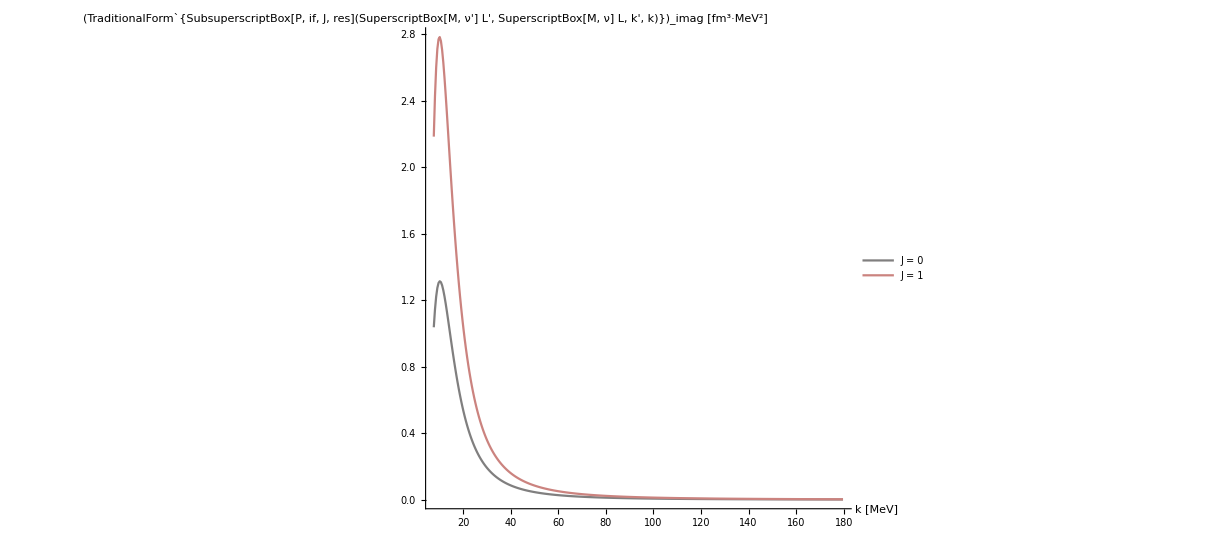
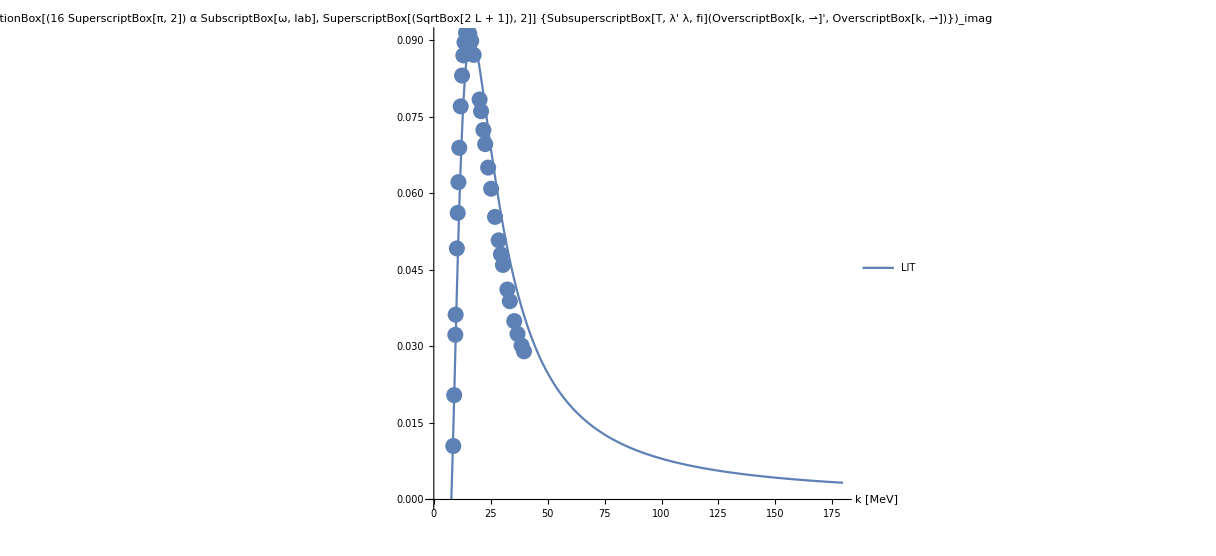
-Graphics- | -Graphics-

```mathematica
Clear[ee,e2];
k0=0.001;k1=180;dK=0.5;
Subscript[k, lab]=Range[Abs[e0],k1,dK];
Ji=Jf=J0;Mi=Ji;Mf=Mi;
Jj=jJtot;
labelj=("J = "<>ToString[#])&/@Jj;
strengthfunctionList=Table[Table[(responseListJ[[nJ]]/.t->ee)/.ee->(e0+kmag),{kmag,Subscript[k, lab]}],{nJ,Range[1,Length[jJtot]]}];

ImPList=2 Pi^2 (-1)^(multipolarity+Jf+Ji) hat[multipolarity] hat[multipolarity] strengthfunctionList;
z=List[];

For[nJ=1,nJ≤Length[Jj],nJ++,(
atmp=ListLinePlot[ImPList[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`{SubsuperscriptBox[P, if, J, res](SuperscriptBox[M, ν'] L', SuperscriptBox[M, ν] L, k', k)})_imag [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];

ImT[Mf_,Mi_,λf_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Jj],nJ++,(
compo=hat[Jj[[nJ]]]^2 ImPList[[nJ,All]];
For[Mm=-multipolarity,Mm≤multipolarity,Mm++,(
For[Mmp=-multipolarity,Mmp≤multipolarity,Mmp++,
(
ampli+=ThreeJSymbol[{Jf,-Mf},{Jj[[nJ]],Mf-Mi},{Ji,Mi}] ThreeJSymbol[{multipolarity,Mm},{multipolarity,Mmp},{Jj[[nJ]],-Mm-Mmp}] WignerD[{multipolarity,Mmp,-λf},0,θ,0] compo;
)];)];)];
Return[(-1)^(1+λf+Jf-Mi)*ampli]
]
fudgi=16;

kinfac=(-1)^(multipolarity+1)(fudgi 16 Pi^2) ((Subscript[k, lab]+e0)/hbarc)/((√(2 multipolarity+1))^2 137.);

DissCross[Mf_,Mi_,λf_,θ_,kinfac_]:=kinfac ImT[Mf,Mi,λf,θ];
lf=1;

Grid[{{
Show[z,PlotRange->All],
Show[ListPlot[Re[DissCross[Jf,Ji,lf,0,kinfac]],PlotRange->{Automatic,{0,Automatic}},LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`-FractionBox[(16 SuperscriptBox[π, 2]) α SubscriptBox[ω, lab], SuperscriptBox[(SqrtBox[2  L + 1]), 2]] {SubsuperscriptBox[T, λ' λ, fi](OverscriptBox[k, ⇀]', OverscriptBox[k, ⇀])})_imag [fm^2] ·("<>ToString[Style[fudgi,Red],TraditionalForm]<>")"}(*,Filling->cycl*),ImageSize->ImgSize,Joined->{True,False},DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotLegends->{"LIT"}],
ListPlot[He3DataFm2,PlotLegends->"σ_tot data"]]
}}]
```

d^5 σ_(He→npp)=(2π)^2 α ω_lab ∑|p_1 q_1Ô(ω)He|^2 d^3(p_1,q_1)δ(p_1^2+3/4 q_1^2-ω)

```mathematica
Clear[solu,wcm,wlab,wcem]
solu=Solve[wcm==wlab (1+2 wlab/mdeu)^(-1/2),wlab];
wl=Simplify[wlab/.solu[[2]]]

kcross=0.5 Sqrt[(wcem+e0-2 mn)(wcem+e0+2 mn)]
```

(wcm^2+√(wcm^2 (mdeu^2+wcm^2)))/mdeu

0.5 √((-1883.81+wcem) (1869.39+wcem))